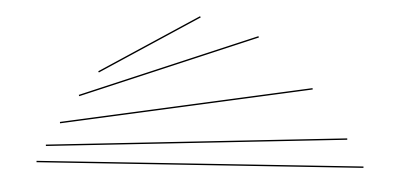

```mathematica
Module[{Rtie1,Rtie2,phaseE},
Rtie1={{0.0976,0.0403},{0.09621,0.0784},{0.09631,0.1316},{0.10011,0.1952},{0.108,0.25073}};
Rtie2={{0.875,0.027},{0.811,0.093},{0.686,0.211},{0.53,0.333},{0.42,0.38(*0.397*)}};

phaseE[x_]=-2.375*x^2+2.375*x-0.2137;


Column[{
Table[x/.Quiet@Solve[phaseE[x]==Rtie1[[n,2]],x][[1]],{n,1,5}],
Table[x/.Quiet@Solve[phaseE[x]==Rtie2[[n,2]],x][[2]],{n,1,5}]
}];

Graphics[{Thick,Table[Line[{
{Table[x/.Quiet@Solve[phaseE[x]==Rtie1[[n,2]],x][[1]],{n,1,5}][[n]],phaseE[Table[x/.Quiet@Solve[phaseE[x]==Rtie1[[n,2]],x][[1]],{n,1,5}][[n]]]},
{Table[x/.Quiet@Solve[phaseE[x]==Rtie2[[n,2]],x][[2]],{n,1,5}][[n]],phaseE[Table[x/.Quiet@Solve[phaseE[x]==Rtie2[[n,2]],x][[2]],{n,1,5}][[n]]]}}],{n,1,5}]
}]

]
```

```mathematica
Manipulate[-2.375*x^2+2.375*x-0.2137,{{x,0.1,""},0.1,0.9,0.01,Appearance->"Labeled"}]
```

```mathematica
{{{{0.12177700813019394,0.8782229918698061},{0.14361463790471213,0.8563853620952878},{0.17656449434888957,0.8234355056511105},{0.22101688411775092,0.7789831158822491},{0.26665363444915313,0.7333463655508469}}}, {{{0.1144450342960846,0.8855549657039155},{0.1523462097218889,0.8476537902781112},{0.23320617067027005,0.76679382932973},{0.359250128540771,0.640749871459229},{0.49541168532258983,0.5045883146774102}}}}
```

```mathematica
Module[{phaseR,R,p1},
phaseR=BezierFunction[{{0.1,0},{0.05,0.69},{0.475,0.46},{0.9,0}},SplineDegree->3];
R=Interpolation[Table[phaseR[i],{i,0.1,0.9,0.05}]];

p1=Show[
Graphics[{
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{1,0},{0,1}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],
{Thick,BezierCurve[{{0.1,0},{0.05,0.69},{0.475,0.46},{0.9,0}},SplineDegree->3]},
{PointSize[0.02],Red,Table[Point[phaseR[i]],{i,0.,1,0.05}]}
}],
Plot[R[z],{z,0.1,0.9},PlotStyle->{Thick,Orange}],
PlotLabel->phaseR[0.1]
];
Export["tie.xlsx",Table[phaseR[i],{i,0,1,0.01}]]
]
```

tie.xlsx

```mathematica
Length[Table[i,{i,0,1,0.05}]]
```

21

```mathematica
Module[{f1,f2},
f1=BezierFunction[{{0.1,0},{0.05,0.69},{0.475,0.46},{0.9,0}},SplineDegree->3];


(*Graphics[{
{Thick,BezierCurve[{{0.1,0},{0.05,0.69},{0.475,0.46},{0.9,0}},SplineDegree->3]},
{PointSize[0.02],Red,Table[Point[f1[i]],{i,0.,1,0.05}]}
}]*)
f2=Table[f1[i],{i,0,1,0.035}];
Column[{Length[f2],f2}]
]
```

29
{{0.1,0.},{0.0964753,0.0690986},{0.0963196,0.131613},{0.0994108,0.18772},{0.105627,0.237597},{0.114845,0.281423},{0.126944,0.319374},{0.1418,0.351628},{0.159293,0.378363},{0.179299,0.399756},{0.201697,0.415984},{0.226364,0.427225},{0.253178,0.433657},{0.282017,0.435456},{0.312759,0.432802},{0.345282,0.42587},{0.379462,0.414839},{0.415179,0.399886},{0.45231,0.381188},{0.490733,0.358924},{0.530325,0.33327},{0.570965,0.304404},{0.612529,0.272504},{0.654897,0.237746},{0.697946,0.20031},{0.741553,0.160371},{0.785596,0.118108},{0.829954,0.073698},{0.874504,0.0273185}}

```mathematica
Module[{f1,f2,round},
f1=BezierFunction[{{0.1,0},{0.05,0.69},{0.475,0.46},{0.9,0}},SplineDegree->3];
f2=Table[f1[i],{i,0,1,0.025}];
round=0.0001;
Interpolation[Round[f2,round]];
(*ListPlot[Round[f2,round],Joined->True,PlotStyle->{Thick,Black},PlotLabel->Length[f2]]*)
Round[f2,round]
]
```

{{0.1,0.},{0.0971,0.05},{0.096,0.0967},{0.0966,0.14},{0.0988,0.1801},{0.1026,0.217},{0.108,0.2507},{0.1148,0.2814},{0.1232,0.3091},{0.133,0.3339},{0.1441,0.3558},{0.1566,0.3749},{0.1704,0.3912},{0.1855,0.4049},{0.2017,0.416},{0.2191,0.4245},{0.2376,0.4306},{0.2572,0.4342},{0.2778,0.4355},{0.2994,0.4345},{0.3219,0.4312},{0.3453,0.4259},{0.3695,0.4184},{0.3946,0.4089},{0.4204,0.3974},{0.4469,0.3841},{0.4741,0.3689},{0.5019,0.3519},{0.5303,0.3333},{0.5593,0.313},{0.5887,0.2911},{0.6185,0.2677},{0.6488,0.2429},{0.6794,0.2167},{0.7104,0.1891},{0.7416,0.1604},{0.773,0.1304},{0.8046,0.0993},{0.8363,0.0672},{0.8681,0.0341},{0.9,0.}}

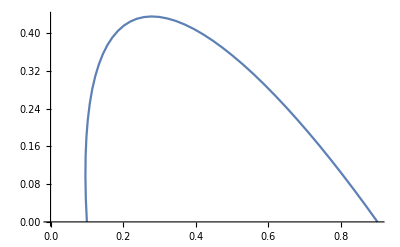

```mathematica
ListPlot[{{0.1,0.},{0.0971,0.05},{0.096,0.09671},{0.0966,0.14},{0.0988,0.1801},{0.10261,0.217},{0.108,0.25073},{0.1148,0.28144},{0.1232,0.30914},{0.133,0.33393},{0.1441,0.3558},{0.15662,0.3749},{0.1704,0.3912},{0.1855,0.40494},{0.20172,0.41604},{0.21912,0.42454},{0.2376,0.43064},{0.25724,0.43423},{0.2778,0.4355},{0.2994,0.4345},{0.3219,0.4312},{0.3453,0.4259},{0.3695,0.4184},{0.3946,0.40894},{0.4204,0.39743},{0.4469,0.3841},{0.4741,0.3689},{0.5019,0.3519},{0.5303,0.33334},{0.5593,0.313},{0.5887,0.2911},{0.6185,0.2677},{0.6488,0.2429},{0.6794,0.2167},{0.7104,0.18912},{0.7416,0.16041},{0.773,0.13042},{0.80461,0.0993},{0.8363,0.06721},{0.86811,0.0341},{0.9,0.}},Joined->True]
```